```mathematica
Clear["Global`*"]
```

NOTE THIS FILE HAS BEEN SUPERSEDED BY 03_fifthorder_220125.nb

# Analytical Solution for u2

## Cory Aitchison - January 2022

Working out to find the coefficients of u^(2) such that L[u^(2)] + N[u^(0) + u^(1)] - N[u^(0)] = 0, up to fifth order terms.

Since we have:
	L[u0] == 0 
	L[u1] + N[u0] == 0 ==> L[u1 + u0] + N[u1 + u0] == N[u1 + u0] - N[u0] 
Therefore we want u2 such that
	L[u2] + N[u1 + u0] - N[u0] == 0

## Set Up

### Miscellaneous

```mathematica
CC[x_]:=Cos[σ x] / Cosh[σ x];
SS[x_]:=Sin[σ x] / Sinh[σ x];
LDE[f_]:=D[f[x],{x,4}] + 4 σ^4 f[x] ;
NDE[f_]:=Γ f[x]^3;
letters = {c, d, e, f};
```

### Ansatz

```mathematica
u[n_]:=x|->Sum[letters[[n]][i]CC[x]^((2n+1)-i) SS[x]^(i), {i, 0, 2n+1}];
u[0] := x |->A CC[x] + B SS[x];
```

### Numerical Values

```mathematica
param = {σ-> 6^(1/4), Γ -> -24};
estimates = {A -> 0.445408, B -> 1.02817};
```

```mathematica
estimates = {A -> 0.4384, B -> 1.017};
```

```mathematica
<<"/Users/cory/Sync/USYD/Denison/Mathematica/PQSHelper.wl"
```

```mathematica
answer1 = AnalyticSolve[LDE[u[1]] +LDE[u[0]]+ NDE[u[0]], 1, x, σ, c];
```

```mathematica
allvalues= Merge[{param, estimates, answer1 /. estimates /. param}, First]
```

<|σ→6^(1/4),Γ→-24,A→0.4384,B→1.017,c[0]→0.15371,c[1]→-0.253315,c[2]→0.137759,c[3]→-0.259133|>

## Solution

### Simplifying Hyp Trig

We first convert the hyperbolic trig terms into sinh and cosh variables, so that Mathematica doesn’t automatically simplify them

```mathematica
eq1 := LDE[u[2]] + NDE[x |->u[0][x] + u[1][x]] - NDE[u[0]];
```

```mathematica
notrig = {
Cosh[_] -> cosh, Sinh[_]->sinh,
Tanh[_] -> sinh / cosh, Coth[_] -> cosh / sinh, 
Sech[_] -> 1/cosh,  Csch[_] -> 1/sinh
};
```

```mathematica
eq2 := eq1 //. notrig // Together;
```

```mathematica
Denominator[eq2]
```

cosh^9 sinh^9

```mathematica
eq3 := Numerator[eq2];
```

We can then use hyp trig identity cosh^2 - sinh^2 = 1 to reduce the terms further.

```mathematica
htrigident = {
cosh^k_-> (1+sinh^2)^(Floor[k/2]) cosh^(Mod[k,2])
};
```

```mathematica
eq4 := eq3 //. htrigident//Expand;
```

### Extracting Coefficients

Now that it is all simplified as far as possible, we can extract the coefficients that give us 13th powers (for the numerator). There will be two: cosh * sinh^12, and sinh^13.

```mathematica
list1 := CoefficientList[eq4, {sinh, cosh}];
```

```mathematica
list2 := {
list1[[13,2]], (* sinh^12 cosh^1 *)
list1[[14,1]]     (* sinh^13 cosh^0 *)
};
```

### Simplifying Trig

These two terms should be identically zero. To find the conditions on c[...], we need to simplify the trig terms using identities:

```mathematica
trigident = {
Cos[x σ]^k_-> (1+Sin[x σ]^2)^(Floor[k/2]) Cos[x σ]^(Mod[k,2])
};
```

```mathematica
list3 :=CoefficientList[list2 /. trigident, {Cos[x σ], Sin[x σ]}];
```

We select only the nonzero coefficients which we need to solve for:

```mathematica
(list4 = list3 // Flatten // Select[Not@*PossibleZeroQ]) // MatrixForm
```

(6 A B Γ c[0]+3 A^2 Γ c[1]+1200 σ^4 d[0]-1080 σ^4 d[1]-120 σ^4 d[2]+720 σ^4 d[3]-480 σ^4 d[4]+120 σ^4 d[5]
12 A B Γ c[0]+6 A^2 Γ c[1]+3 B^2 Γ c[1]+6 A B Γ c[2]+3 A^2 Γ c[3]+3600 σ^4 d[0]-720 σ^4 d[1]-240 σ^4 d[2]-80 σ^4 d[3]-1200 σ^4 d[4]+2800 σ^4 d[5]
6 A B Γ c[0]+3 A^2 Γ c[1]+3 B^2 Γ c[1]+6 A B Γ c[2]+3 A^2 Γ c[3]+3 B^2 Γ c[3]+2400 σ^4 d[0]+384 σ^4 d[1]-544 σ^4 d[3]-480 σ^4 d[4]+2624 σ^4 d[5]
3 A^2 Γ c[0]-56 σ^4 d[0]-240 σ^4 d[1]+256 σ^4 d[2]-120 σ^4 d[3]+24 σ^4 d[4]
6 A^2 Γ c[0]+3 B^2 Γ c[0]+6 A B Γ c[1]+3 A^2 Γ c[2]+2448 σ^4 d[0]-240 σ^4 d[1]-1008 σ^4 d[2]-240 σ^4 d[3]+1488 σ^4 d[4]-1200 σ^4 d[5]
3 A^2 Γ c[0]+3 B^2 Γ c[0]+6 A B Γ c[1]+3 A^2 Γ c[2]+3 B^2 Γ c[2]+6 A B Γ c[3]+2624 σ^4 d[0]+480 σ^4 d[1]-544 σ^4 d[2]+384 σ^4 d[4]-2400 σ^4 d[5])

### Solution

```mathematica
answer = Solve[list4 == 0, (i|->d[i])/@ Range[0,5]][[1]] // Simplify
```

{d[0]→-1/(66560 σ^4)Γ (A^2 (95 c[0]+53 c[1]+37 c[2]+35 c[3])+2 A B (53 c[0]+37 c[1]+35 c[2]+39 c[3])+B^2 (37 c[0]+35 c[1]+39 c[2]+85 c[3])),d[1]→1/(66560 σ^4)Γ (2 A B (53 c[0]-c[1]-33 c[2]-55 c[3])+A^2 (265 c[0]+53 c[1]-c[2]-33 c[3])-B^2 (c[0]+33 c[1]+55 c[2]+195 c[3])),d[2]→1/(33280 σ^4)Γ (B^2 (5 c[0]-17 c[1]-33 c[2]-175 c[3])+2 A B (c[0]+5 c[1]-17 c[2]-33 c[3])+A^2 (-185 c[0]+c[1]+5 c[2]-17 c[3])),d[3]→1/(33280 σ^4)Γ (B^2 (17 c[0]+5 c[1]-c[2]-185 c[3])-2 A B (33 c[0]-17 c[1]-5 c[2]+c[3])+A^2 (175 c[0]-33 c[1]+17 c[2]+5 c[3])),d[4]→1/(66560 σ^4)Γ (B^2 (-33 c[0]+c[1]+53 (c[2]-5 c[3]))+A^2 (-195 c[0]+55 c[1]-33 c[2]+c[3])+2 A B (55 c[0]-33 c[1]+c[2]+53 c[3])),d[5]→1/(66560 σ^4)Γ (B^2 (35 c[0]-37 c[1]+53 c[2]-95 c[3])+A^2 (85 c[0]-39 c[1]+35 c[2]-37 c[3])+2 A B (-39 c[0]+35 c[1]-37 c[2]+53 c[3]))}

```mathematica
answer /. answer1 // FullSimplify
```

{d[0]→((-95 A^5+86 A^4 B+98 A^3 B^2+352 A^2 B^3+273 A B^4+266 B^5) Γ^2)/(21299200 σ^8),d[1]→-((86 A^5+671 A^4 B+712 A^3 B^2+798 A^2 B^3+626 A B^4-273 B^5) Γ^2)/(21299200 σ^8),d[2]→((49 A^5+356 A^4 B+50 A^3 B^2+532 A^2 B^3-399 A B^4+176 B^5) Γ^2)/(10649600 σ^8),d[3]→-((176 A^5+399 A^4 B+532 A^3 B^2-50 A^2 B^3+356 A B^4-49 B^5) Γ^2)/(10649600 σ^8),d[4]→((273 A^5+626 A^4 B-798 A^3 B^2+712 A^2 B^3-671 A B^4+86 B^5) Γ^2)/(21299200 σ^8),d[5]→-((266 A^5-273 A^4 B+352 A^3 B^2-98 A^2 B^3+86 A B^4+95 B^5) Γ^2)/(21299200 σ^8)}

```mathematica
answer //. allvalues
```

{d[0]→0.000374713,d[1]→-0.000185209,d[2]→0.000195959,d[3]→-0.000252015,d[4]→-0.0000892336,d[5]→-0.00011163}

## Plots

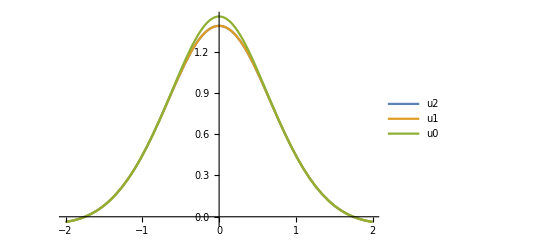

```mathematica
Plot[
{
u[0][x] + u[1][x] + u[2][x] //. answer //. allvalues ,
u[0][x]+u[1][x] //. allvalues,
u[0][x] //. allvalues 
},
{x,-2,2}, 
PlotLegends->{"u2", "u1", "u0"}
]
```